```mathematica
A={{1,-2,3,4,2},{1,-2,5,5,3},{-1,2,-1,-4,2}};
```

```mathematica
TableForm[A]
```

1 | -2 | 3 | 4 | 2
1 | -2 | 5 | 5 | 3
-1 | 2 | -1 | -4 | 2

```mathematica
TableForm[RowReduce[A]]
```

1 | -2 | 0 | 0 | 8
0 | 0 | 1 | 0 | 2
0 | 0 | 0 | 1 | -3

```mathematica
Solve[
a-2b+3c+4d==2&&
a-2b+5c+5d==3&&
-a+2b-c-4d==2,
{a,b,c,d}
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{b→-4+a/2,c→2,d→-3}}

```mathematica
f[x_,n_]:=4/π Sum[1/(2*k-1)*Sin[(2k-1)*π*x],{k,1,n}];
```

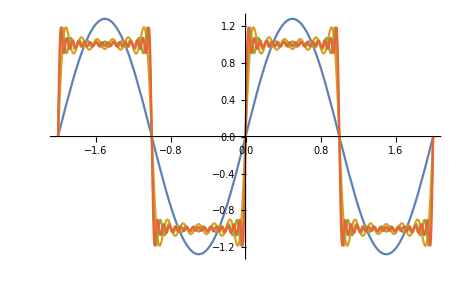

```mathematica
fset=Table[f[x,n],{n,1,20,5}];
Plot[fset,{x,-2,2}]
```

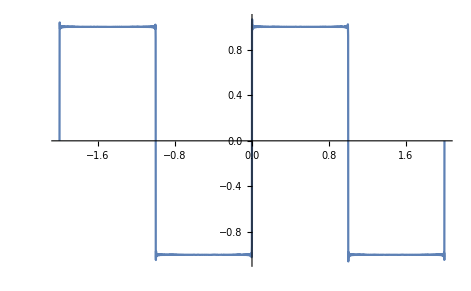

```mathematica
Plot[f[x,1000],{x,-2,2}]
```